## Import Data

```mathematica
(*set a random seed for training/test set generation for replicability*)
SeedRandom[1841]; 
SetDirectory@NotebookDirectory[];

(* Helper functions *)
<<"src/platereader.wl"
<<"src/import_scripting.wl"
<<"src/emd.wl"

(*load training data *)
trainingData = Flatten@Map[importDirectory]@{"data/2023_07_20_PH_Indicator","data/2023_07_21_PH_Indicator"};

Length[%]
```

898

Comments:  The formatting of the test data requires some manual handling; this should be discussed

```mathematica
(* load test amphiphile data *)
testData=With[
{pH = Import[
"data/Amphiphile_Absorbance_test/07262023_10carbons_RealPH_Values.xlsx",
{"Data",1,Join[Range[5,12],Range[17,24]],2;;13},
"EmptyField"->Missing[]] // Flatten //ReplaceAll[ "Empty"->Missing[]],
spectra = importPlateReaderFilesFromDirectory["data/Amphiphile_Absorbance_test/"]},
output[spectra, pH]];

Length[%]
```

175

## Model Testing

### GBT:

Based on previous work (2023.07.20_expanded_dataset.nb), Gradient Boosted Trees trained on the complete (non-dimensional reduced) dataset had the best performance for predicting pH.

```mathematica
gbt = Predict[trainingData,Method->"GradientBoostedTrees"];

Information[gbt]
```

Predictor information
Data type | NumericalVector (××41)
Standard deviation | 0.631 ± 0.073
Method | GradientBoostedTrees
Single evaluation time | 5.48 ms/example
Batch evaluation speed | 12.2 examples/ms
Loss | 167. ± 20.
Model memory | 465. kB
Training examples used | 898 examples
Training time | 6.68 s
 |

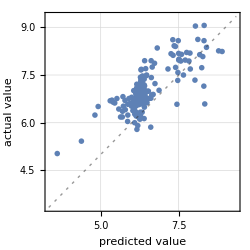
Predictor Measurements
Predictor method | GradientBoostedTrees
Number of test examples | 175
Standard deviation | 0.73 ± 0.03
Standard deviation baseline | 0.701 ± 0.04
R-squared | -0.0822 ± 0.15
Mean cross entropy | 39.6 ± 3.4
Single evaluation time | 7.48 ms/example
Batch evaluation speed | 529. examples/s
-Graphics- |

```mathematica
reportGBT=PredictorMeasurements[gbt,testData]
```

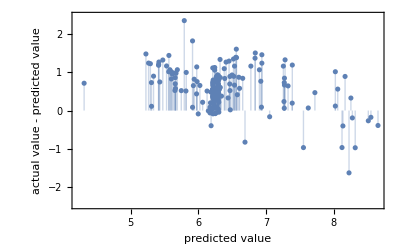

```mathematica
reportGBT["ResidualPlot"]
```

```mathematica
reportGBT["MeanDeviation"]
```

0.691739

### Nearest Neighbor

PredictorFunction[…]

Predictor information
Data type | NumericalVector (××41)
Standard deviation | 0.682 ± 0.096
Method | NearestNeighbors
Single evaluation time | 3.02 ms/example
Batch evaluation speed | 54. examples/ms
Loss | 0.601 ± 0.1
Model memory | 398. kB
Training examples used | 898 examples
Training time | 371. ms
 |

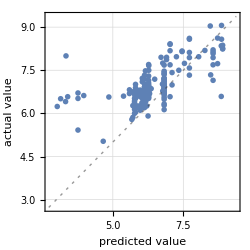
Predictor Measurements
Predictor method | NearestNeighbors
Number of test examples | 175
Standard deviation | 0.985 ± 0.094
Standard deviation baseline | 0.701 ± 0.04
R-squared | -0.974 ± 0.44
Mean cross entropy | 4.26 ± 0.95
Single evaluation time | 3.25 ms/example
Batch evaluation speed | 719. examples/s
-Graphics- |

```mathematica
nn = Predict[trainingData,Method->"NearestNeighbors"]
Information[nn]
nnReport = PredictorMeasurements[nn,testData]
```

```mathematica
nnReport["MeanDeviation"]
```

0.705886

### Optimal Transport Classifier

```mathematica
ot = Nearest[trainingData,DistanceFunction->emd]
```

NearestFunction[…]

This takes about 10 minutes on the old laptop...

```mathematica
pred=ParallelMap[ot,testData[[All,1]]];
```

0.70.6

0.400281

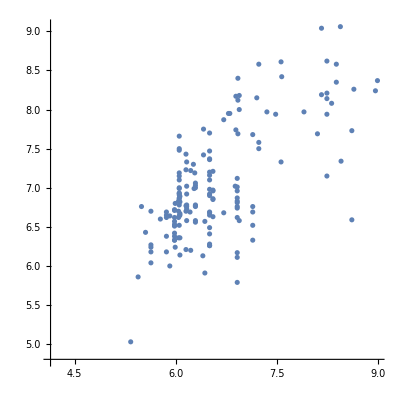

```mathematica
obs=testData[[All,2]];

mad = Around@Abs[obs-Flatten[pred]]
Correlation[obs,Flatten[pred]]^2

ListPlot[
Transpose[{Flatten[pred],obs}],
AspectRatio->1]
```

## Hypothesis: Domain Shift can be resolved by building a new model on these data

Test:  Perform 5-fold cross validation on the (amphiphile) test data and assess performance;  as determined in earlier work (2023.07.18_pH_spectroscopy.nb), EMD is the best when we have limited data

```mathematica
validation[model_NearestFunction,validationData_List]:=With[
{obs=validationData[[All,2]],
predicted = model/@validationData[[All,1]]//Flatten},
{Mean@Abs[obs-predicted], Correlation[obs,predicted]^2}]

(* perform 5-fold cross validation of the EMD model *)
cvEMDSummary=ResourceFunction["CrossValidateModel"][
testData,
Nearest[#,DistanceFunction->emd]&, (*model definition*)
"ValidationFunction"->validation,
"ParallelQ"->True];

(* collect summary statistics *)
Around/@Transpose@%[[All,"ValidationResult"]]
```

{0.380.04,0.480.18}

Indeed:  We can reduce the error to around MAE = 0.38 pH units if we use this new data for model construction

## Conclusions/Next-Steps

All of the methods (GBT, NN, OT) that did well on our previous datasets seem to have poor descriptive power for this system.

MAE is about 0.7 pH units for all methods—about 3x what we saw before.

This can be reduced by half (0.38 pH units) if we build a OT model on these new data—which is evidence of a domain shift (i.e., a small amount of data from the new domain is better than a larger pool of data from the old domain)

What might be causing a distribution shift in the data?

Effect of amphiphiles on spectra?

Measurement differences?

Do we care?

Housekeeping:  Data-formatting differences—which require some manual wrangling—work towards standardizing format